# Journal citation fitting

## Data

```mathematica
citedMatWithJnameString=Import["/Users/amanokou/TEST_COLLECTION/Bibliometrics/JournalCitationClustering/RAW/JCR_cited_2004.mat","CSV"];
```

```mathematica
citedMatWithJnameStringSplited= Map[StringSplit[#," "]&,citedMatWithJnameString];
```

```mathematica
citedMatWithJnameStringSplited//Dimensions
```

{5964,1,5965}

```mathematica
Jnames=Map[#[[1,1]]&,citedMatWithJnameStringSplited];
```

```mathematica
citedMatString=Map[#[[1,2;;5965]]&,citedMatWithJnameStringSplited];
```

```mathematica
citedMatString//Dimensions
```

{5964,5964}

```mathematica
citedMat=ToExpression[citedMatString];
```

```mathematica
Map[Head[#]&,citedMat,{2}]//Flatten//Union
```

{Integer}

```mathematica
totalCited=Map[Tr[#]&,citedMat];
```

```mathematica
totalCitedOrder=Ordering[totalCited,All,Greater];
```

```mathematica
totalCitedSort=totalCited[[Ordering[totalCited,All,Greater]]];
```

```mathematica
rankVSTotalCited=Table[{n,totalCitedSort[[n]]},{n,5964}];
```

```mathematica
totalCitedSortLog=Log[totalCitedSort]//N;
```

```mathematica
totalCitedSortLogLog=Table[{Log[n]//N,totalCitedSortLog[[n]]},{n,Length[totalCitedSortLog]}]
```

{{0.,12.0341},{0.693147,11.6962},{1.09861,11.692},{1.38629,11.5957},{1.60944,11.3402},«5955»,{8.69299,0.},{8.69316,0.},{8.69333,-∞},{8.6935,-∞}}

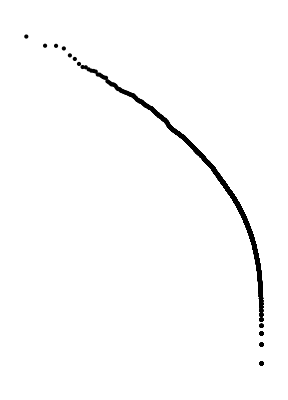

```mathematica
Graphics[Drop[Map[Point[#]&,totalCitedSortLogLog],-2]]
```

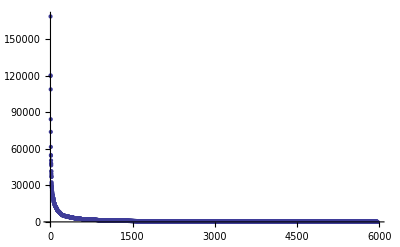

```mathematica
ListPlot[totalCitedSort,PlotRange->All]
```

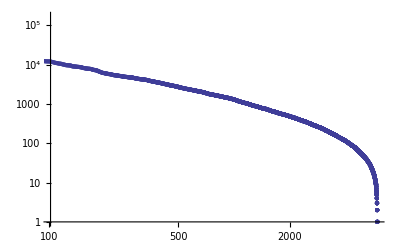

```mathematica
ListLogLogPlot[totalCitedSort,PlotRange->All]
```

## Fitting

### zipf fit

```mathematica
zipf[rank_,a_,c_]:=c*rank^(-a)
```

```mathematica
cited=c*rank^(-a)
```

c rank^-a

```mathematica
fitted=FindFit[totalCitedSort[[1;;5962]],zipf[rank,a,c],{a,c},rank]
```

{a→0.669646,c→207611.}

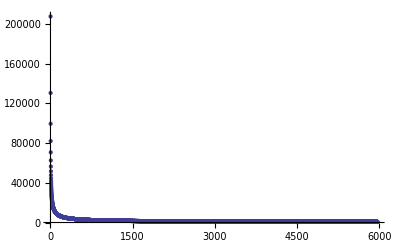

```mathematica
ListPlot[Table[zipf[n,a,c]/.fitted,{n,5964}],PlotRange->All]
```

```mathematica
loglogpoint=Table[{Log[n]//N,Log[zipf[n,a,c]/.fitted]},{n,5964}]
```

{{0.,12.2434},{0.693147,11.7793},{1.09861,11.5077},{1.38629,11.3151},«5957»,{8.69316,6.42208},{8.69333,6.42197},{8.6935,6.42186}}

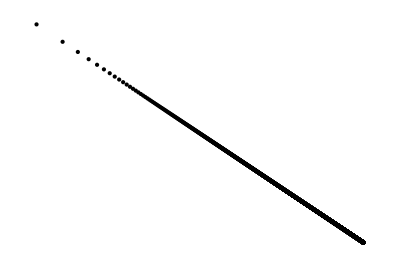

```mathematica
Graphics[Map[Point[#]&,loglogpoint]]
```

```mathematica
totalCitedSort[[1]]
```

168405

Zipfの法則は、「ユリシーズ」 に現れる単語の出現頻度を多い順に並べると、出現頻度は概ね順位に反比例することを発見したのが始まりらしい。Zipfは "Human Behavior and the Principle of Least Effort" という本を書いて、都市の人口とかにも当てはまるとか言ったらしいけど、本は読んでないので、実際何が書いてあるかは知らない。Zipfの法則は、色々な現象で普遍的に観察される現象だということになってるらしい。当たり前の話だけど、単調減少する関数fで、x -> ∞でf (x) -> 0 になるようなものを考えると、fがある程度緩やかに減衰するなら、漸近的にf (x) ～c*x^aと書けて、両辺のlogとれば、log f = log (c) + a*log (x) なので、両対数グラフを最小二乗法でfittingすれば、とりあえず、指数aと係数cは求まってしまう。偶然aが - 1 付近になってしまうことも多々あるだろう。そんなわけで、きちんと検定してないものはZipf則に従ってると言えるか怪しい。

### logit fit

```mathematica
lgF[maxrank_,a_,b_,rank_]:=E^Log[b(maxrank-b((rank)^(a)))]
```

ランクの調整なし ↑

```mathematica
lgF[maxrank_,a_,b_,rank_]:=E^Log[b(maxrank-b((rank-1)^(a)))]
```

ランクの調整あり ↑

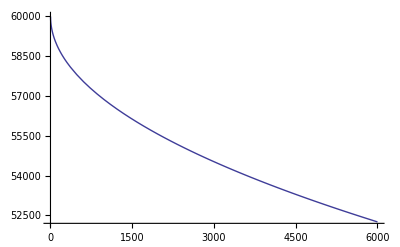

```mathematica
Plot[lgF[6000,0.5,10,rank],{rank,1,6000}]
```

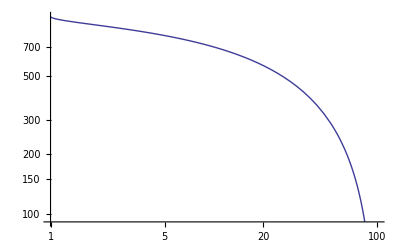

```mathematica
LogLogPlot[lgF[100,0.5,10,rank],{rank,1,100}]
```

```mathematica
lgF[100,0.5,10,1]
```

1000.

```mathematica
E^(Log[10(100-10(x^(0.5)))])/.x->99
```

5.01256

```mathematica
E^(Log[10(100-10(x^(0.5)))])/.x->1
```

900.